# Kinematic Interaction: formulation in terms of Path-Independent Integrals (PIIs) for the long-wavelength regime

Joaquin Garcia-Suarez, 2019 (All rights reserved)

This notebook details the procedure to obtain the final result in Chapter 6: an approximation to kinematic interaction based on PII and the long-wavelength assumption, supported by a Winkler stress model.

## Functions to represent Balance of Configurational Forces

Expansion in terms of r

Rotation at the base of the structure (I will not use the tilde in the notebook, but understand that the following variables correspond to those with tilde in the text).

```mathematica
θ[r_,N_]:=Sum[Subscript[θ, n]*r^n,{n,2,N}];
```

```mathematica
K[r_,N_]:=Sum[Subscript[K, n]*r^n,{n,0,N}];
```

Horizontal Balance of Configurational Forces

The next function equalized to zero yields the equation for balance of configurational forces, eq.(6.17a) (note that, in this notebook, I will use C in lieu c^2). HRCF=horizontal resultant of configurational forces.

```mathematica
HRCF[r_,N_]:=K[r,N]^2*C*(1+(2 θ[r,N])/r^2+θ[r,N]^2/3-((2+r^2) θ[r,N] Cos[r])/r^2+1/2 Cos[2 r]-(3 Sin[2 r])/(4 r))+r^2*(Cos[r]^2-θ[r,N]*Cos[r]+θ[r,N]^2*(B^2+1/3))-K[r,N]*C*θ[r,N]^2*B^2-r*Cos[r]*Sin[r]
```

Vertical Balance of Configurational Forces

Likewise, VRCF=vertical resultant of configurational forces. The following corresponds to eq.(6.17b):

```mathematica
VRCF[r_,N_]:=(K[r,N]^2*C+r^2)*θ[r,N]^2*B^3/3+r^2*Cos[r]^2*B-2*θ[r,N]*K[r,N]*C*(θ[r,N]/2-Cos[r]+Sin[r]/r)-r^2*B
```

## Perturbation Series for the Balance Equations

The small parameter used to expand the variables is r=ωh/c_s

Expand the Balance Equations

## Horizontal Balance of Configurational Forces

Expand the RHS of each balance and equalize to zero each power of r necessary:

```mathematica
Series[HRCF[r,5],{r,0,5}]
```

1/60 (-20+8 C K_0^2-60 θ_2+25 C K_0^2 θ_2-60 B^2 C K_0 θ_2^2+20 C K_0^2 θ_2^2) r^4+1/60 (16 C K_0 K_1+50 C K_0 K_1 θ_2-60 B^2 C K_1 θ_2^2+40 C K_0 K_1 θ_2^2-60 θ_3+25 C K_0^2 θ_3-120 B^2 C K_0 θ_2 θ_3+40 C K_0^2 θ_2 θ_3) r^5+O[r]^6

## Expansion of Vertical Balance of Configurational Forces

```mathematica
Series[VRCF[r,5],{r,0,5}]
```

1/3 (-3 B-2 C K_0 θ_2-3 C K_0 θ_2^2+B^3 C K_0^2 θ_2^2) r^4+1/3 (-2 C K_1 θ_2-3 C K_1 θ_2^2+2 B^3 C K_0 K_1 θ_2^2-2 C K_0 θ_3-6 C K_0 θ_2 θ_3+2 B^3 C K_0^2 θ_2 θ_3) r^5+O[r]^6

## Evaluation of the simplified model

Auxiliary Parameters

The ration between P and S waves velocities.

```mathematica
c[ν_]:=Sqrt[(2(1-ν))/(1-2ν)]
```

Function to find K_0 and θ_2:

sol3 yields the numerical solution given a certain value of B/h (referred just as B in the following) and by C, which recall refers to c^2:

```mathematica
sol3[B_,C_]:=NSolve[{-3 B-2 C Subscript[K, 0] Subscript[θ, 2]-3 C Subscript[K, 0] Subscript[θ, 2]^2+B^3 C Subscript[K, 0]^2 Subscript[θ, 2]^2==0,-20+8 C Subscript[K, 0]^2-60 Subscript[θ, 2]+25 C Subscript[K, 0]^2 Subscript[θ, 2]-60 B^2 C Subscript[K, 0] Subscript[θ, 2]^2+20 C Subscript[K, 0]^2 Subscript[θ, 2]^2==0},{Subscript[K, 0],Subscript[θ, 2]},Reals]
```

Evaluation for certain combinations of parameters

The results that are obtained next are used to evaluate the Figure 6.2. A value of 0.4 is chosen for the Poisson’s ratio to generate all plots:

```mathematica
NU=0.4;
```

1) First, ν=0.4 and B/h=1/4 :

```mathematica
B=1/4; sol3[B,c[NU]^2]
```

{{K_0→-0.636657,θ_2→0.086824},{K_0→0.640521,θ_2→-0.118608},{K_0→0.375069,θ_2→-0.318544}}

Among the possible solutions, pick the one that yields the most negative slope concurrently with positive impedance (in this case, the third case).

2) ν=0.4 and B/h=1/2 :

```mathematica
B=1/2; sol3[B,c[NU]^2]
```

{{K_0→6.61475,θ_2→-0.901018},{K_0→-0.611768,θ_2→0.163304},{K_0→0.747973,θ_2→-0.285932}}

3) ν=0.4 and B/h=1 :

```mathematica
B=1; sol3[B,c[NU]^2]
```

{{K_0→1.31035,θ_2→-0.239079},{K_0→-0.428161,θ_2→0.360782}}

4) ν=0.4 and B/h=2 :

```mathematica
B=2; sol3[B,c[NU]^2]
```

{{K_0→-0.00637419,θ_2→6.85051},{K_0→1.71223,θ_2→0.345134},{K_0→1.66423,θ_2→-0.163159}}

## Display the results in plots

Function proposed by Conti et al. (2017)

```mathematica
a4[B_]:=1/(1+1.7*(2*B)^1.62);
```

```mathematica
Conti[B_,r_]:=a4[B]*(1-Cos[r])
```

Comparison plots

First Plot: ν=0.4 and B/h=1/4

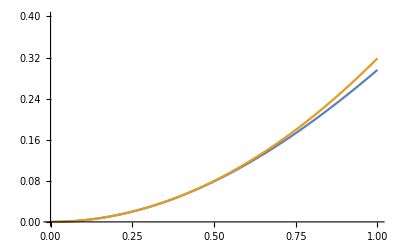

```mathematica
B=1/4;P=0.31854415069403763;Plot[{Conti[B,r],P*r^2},{r,0,1},PlotRange->{{0,1},{0,0.4}}]
```

Second Plot: ν=0.4 and B/h=1/2

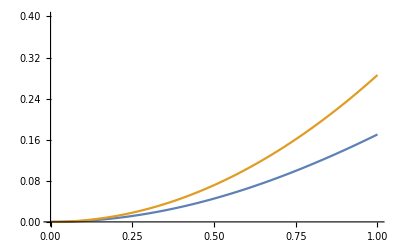

```mathematica
B=1/2;P=0.28593244181956845;Plot[{Conti[B,r],P*r^2},{r,0,1},PlotRange->{{0,1},{0,0.4}}]
```

Third Plot: ν=0.4 and B/h=1

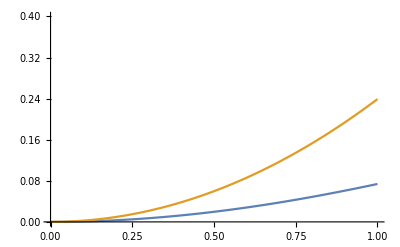

```mathematica
B=1;P=0.23907851949125286;Plot[{Conti[B,r],P*r^2},{r,0,1},PlotRange->{{0,1},{0,0.4}}]
```

Fourth (and last) Plot: ν=0.4 and B/h=2

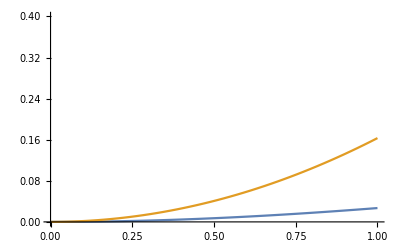

```mathematica
B=2;P=0.16315886833959006;Plot[{Conti[B,r],P*r^2},{r,0,1},PlotRange->{{0,1},{0,0.4}}]
```